## Lab 5

Find the inflection points of the function f(x)=(x-2)^3(x+1)^2, and plot f(x) together with its tangent lines at these points for -2≤x≤3.

{2,1/10 (2-3 √6),1/10 (2+3 √6)}

{2.,-0.534847,0.934847}

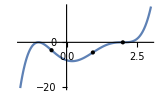

```mathematica
f[x_]:=(x-2)^3(x+1)^2
g[x_]=f''[x];
xs=x/.Solve[g[x]==0&&-2≤x≤3,x]
%//N
Show[{
Plot[f[x],{x,-2,3},PlotRange->Automatic,ImageSize->160],
Graphics[{PointSize[Medium],Point[{xs[[1]],f[xs[[1]]]}]}],
Graphics[{PointSize[Medium],Point[{xs[[2]],f[xs[[2]]]}]}],
Graphics[{PointSize[Medium],Point[{xs[[3]],f[xs[[3]]]}]}]
},PlotRange->All]
```

```mathematica
ExploreTangentLine[func_,{x_,xmin_,xmax_},plotRange_] :=
Manipulate[
 Module[
{f, fPrime},
f[X_]=func/.x->X;
fPrime[X_]=f'[X];

Show[{
Plot[{f[x],fPrime[x],f[x0]+fPrime[x0](x-x0)},{x,xmin,xmax},PlotStyle->{{},{Dashed, Gray},{}},plotRange,ImageSize->320],
Graphics[{Red,PointSize[Medium],Point[{x0,f[x0]}]}]
}]],
{{x0,xmin+(xmax-xmin)/3,Style[Subscript[x, 0]]},xmin,xmax}
]
ExploreTangentLine[f[x],{x,-2,3},PlotRange->Automatic]
```

For sin x, find the equation of the secant line through (-(5π)/6,-1/2) and ((5π)/6,1/2). Then, plot the function together with the secant line for -π≤x≤π.

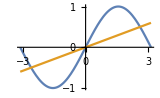

The secant line is y = (3 (x+(5 π)/6))/(5 π)-1/2

```mathematica
f[x_]:=Sin[x]
g[x_]:=Module[{x1=-(5Pi)/6,x2=(5Pi)/6},f[x1]+(f[x2]-f[x1])/(x2-x1)(x-x1)] (* secant line*)
Plot[{f[x],g[x]},{x,-Pi,Pi},PlotRange->Automatic,ImageSize->160]
Print["The secant line is y = ", TraditionalForm[g[x]]]
```

For f(x)=e^x, letting h=0.01 and h=0.001, respectively, compute the forward, backward, and central difference quotients at x=1, and compare with the exact value of f'(1).

```mathematica
f[x_]:=ⅇ^x;
h=0.01;
x0=1;
exact=f'[x0]
```

ⅇ

```mathematica
(f[x0+h]-f[x0])/h
```

2.73192

```mathematica
Abs[%-exact]
```

0.0136368

```mathematica
(f[x0]-f[x0-h])/h
```

2.70474

```mathematica
Abs[%-exact]
```

0.0135462

```mathematica
(f[x0+h]-f[x0-h])/(2h)
```

2.71833

```mathematica
Abs[%-exact]
```

0.0000453049

```mathematica
f[x_]:=ⅇ^x;
h=0.001;
x0=1;
exact=f'[x0]
```

ⅇ

```mathematica
(f[x0+h]-f[x0])/h
```

```mathematica
2.7196414225332255
Abs[%-exact]
```

2.71964

```mathematica
0.0013595940741804036
(f[x0+h]-f[x0-h])/(2h)
```

0.00135959

2.71828

```mathematica
Abs[%-exact]
```

4.53047×10^-7

```mathematica
AccountingForm[4.53046678838831*^-7]
```

0.000000453047

All outputs gave a pretty close approximation to the actual value of e which is 2.718.  The central difference quotient gave the most accurate output.

With h=0.1, use the central difference quotient to approximate the derivative, find the tangent line of f(x)=cos x at x=π/4, and plot the function together with the tangent line over [-π,π].

```mathematica
f[x_]:=Cos[x];
h=0.1;
x0=π/4;
exact=f'[x0]
```

-1/(√2)

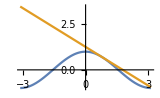

```mathematica
f[x_]:=Cos[x]
g[x_,x0_]:=f[x0]+f'[x0](x-x0)
Plot[{f[x],g[x,Pi/4]},{x,-Pi,Pi},PlotRange->Automatic,ImageSize->160]
```

Find all x where the tangent lines of f(x)=(x+1)^2(x-1) are parallel to y=2x. Then, plot the function together with the tangent lines at these points for -2≤x≤2.

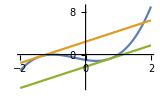

```mathematica
f[x_]:=(x+1)^2(x-1)
g[x_,x0_]:=f[x0]+f'[x0](x-x0)
Plot[{f[x],g[x,(-1-√10)/3], g[x,(-1+√10)/3 ]},{x,-2,2},PlotRange->Automatic,ImageSize->160]
```

Given that f(x)=x/(1+x), find f'(x), f''(x),f'''(x),⋯ at x=0. Can you find a pattern for the obtained sequence? Use Table and your pattern to generate a list and determine if your pattern is correct.

```mathematica
f[x_]:=x/(1+x)
Table[D[f[x],{x,n}],{n,1,20}]//Simplify
```

{1/(1+x)^2,-2/(1+x)^3,6/(1+x)^4,-24/(1+x)^5,120/(1+x)^6,-720/(1+x)^7,5040/(1+x)^8,-40320/(1+x)^9,362880/(1+x)^10,-3628800/(1+x)^11,39916800/(1+x)^12,-479001600/(1+x)^13,6227020800/(1+x)^14,-87178291200/(1+x)^15,1307674368000/(1+x)^16,-20922789888000/(1+x)^17,355687428096000/(1+x)^18,-6402373705728000/(1+x)^19,121645100408832000/(1+x)^20,-2432902008176640000/(1+x)^21}

```mathematica
%/.x-> 0
```

{1,-2,6,-24,120,-720,5040,-40320,362880,-3628800,39916800,-479001600,6227020800,-87178291200,1307674368000,-20922789888000,355687428096000,-6402373705728000,121645100408832000,-2432902008176640000}

```mathematica
Table[{(-1)^(n-1)n!},{n,1,10}]
```

{{1},{-2},{6},{-24},{120},{-720},{5040},{-40320},{362880},{-3628800}}

```mathematica
%//Flatten
```

{1,-2,6,-24,120,-720,5040,-40320,362880,-3628800}

Given that f(x)=sin x cos x, find f'(x), f''(x),f'''(x),⋯ at x=π/2. Can you find a pattern for the obtained sequence? Use Table and your pattern to generate a list and determine if your pattern is correct.

```mathematica
f[x_]:=Sin[x]Cos[x]
Table[D[f[x],{x,n}],{n,1,20}]//Simplify
```

{Cos[2 x],-4 Cos[x] Sin[x],-4 Cos[2 x],8 Sin[2 x],16 Cos[2 x],-64 Cos[x] Sin[x],-64 Cos[2 x],256 Cos[x] Sin[x],256 Cos[2 x],-512 Sin[2 x],-1024 Cos[2 x],4096 Cos[x] Sin[x],4096 Cos[2 x],-8192 Sin[2 x],-16384 Cos[2 x],65536 Cos[x] Sin[x],65536 Cos[2 x],-262144 Cos[x] Sin[x],-262144 Cos[2 x],524288 Sin[2 x]}

```mathematica
%/.x-> Pi/2
```

{-1,0,4,0,-16,0,64,0,-256,0,1024,0,-4096,0,16384,0,-65536,0,262144,0}

```mathematica
Table[{(-1)^n(-4^n),0 }, {n,0,9}]
```

{{-1,0},{4,0},{-16,0},{64,0},{-256,0},{1024,0},{-4096,0},{16384,0},{-65536,0},{262144,0}}

```mathematica
%//Flatten
```

{-1,0,4,0,-16,0,64,0,-256,0,1024,0,-4096,0,16384,0,-65536,0,262144,0}